This notebook examines the pitchfork bifurcation of the growth rate equation f = μ x^2 - x^4+λ with λ=0.  The parameter λ = (-Pm Ga/Sn).  We consider cases with a non-porous isothermal substrate

For λ = 0, μ = 0 and μ = -1 plots match.

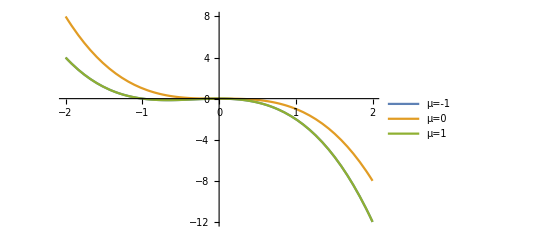

```mathematica
f=μ x^2 -x^3+λ;
λ=0.;
Plot[{f/.μ->-1,f/.μ->0,f/.μ->-1},{x,-2,2},PlotLegends->{"μ=-1","μ=0","μ=1"},PlotRange->All]
```

Bifurcation plot

{x→0.,x→0.,x→-1. √μ,x→√μ}

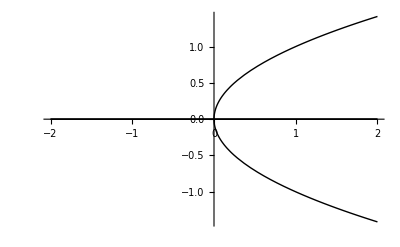

```mathematica
Clear[roots,μ,x,λ];
λ=0.;
roots=Quiet[Solve[μ x^2 - x^4+λ==0,x]//Flatten]
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{μ,-2,2},PlotStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}]
```

Potential plot

x^5/5-(x^3 μ)/3

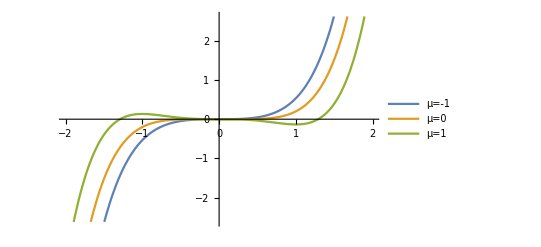

```mathematica
Clear[V,μ,λ,x];
λ=0.;
V=-Integrate[μ x^2 -x^4+λ,x]
Plot[{V/.μ->-1,V/.μ->0,V/.μ->1},{x,-2,2},PlotLegends->{"μ=-1","μ=0","μ=1"}]
```

Attractors? Repellors? Half - stable points?

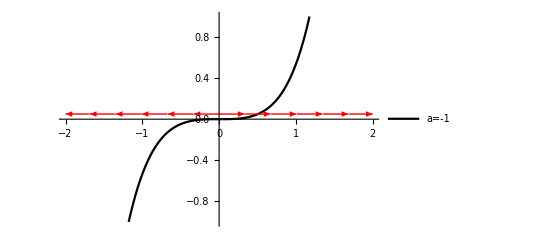

```mathematica
Clear[V,μ,λ,x];
λ=0.;
V=-Integrate[μ x^2 -x^4+λ,x];
g11=Show[Plot[{V/.μ->-1},{x,-2,2},PlotLegends->{"a=-1"},PlotStyle->{Thick,Black},PlotRange->{All,{-1,1}}],
StreamPlot[{V/.μ->-1,0},{x,-2,2},{y,0.,0.1},StreamStyle->{Thick,Red}]
]
```

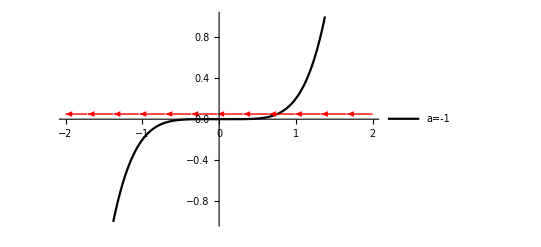

```mathematica
Clear[V,μ,λ,x];
λ=0.;
V=-Integrate[μ x^2 -x^4+λ,x];
g12=Show[Plot[{V/.μ->0},{x,-2,2},PlotLegends->{"a=-1"},PlotStyle->{Thick,Black},PlotRange->{All,{-1,1}}],
StreamPlot[{V/.μ->0,0},{x,-2,2},{y,0.,0.1},StreamStyle->{Thick,Red}]
]
```

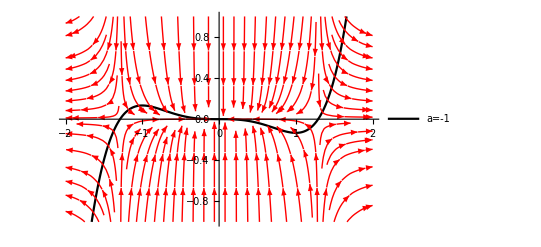

```mathematica
Clear[V,μ,λ,x];
λ=0.;
V=-Integrate[μ x^2 -x^4+λ,x];
g13=Show[Plot[{V/.μ->1},{x,-2,2},PlotLegends->{"a=-1"},PlotStyle->{Thick,Black},PlotRange->{All,{-1,1}}],
StreamPlot[{V/.μ->1,-y},{x,-2,2},{y,-1,1},StreamStyle->{Thick,Red}]
]
```

Roots of potential function

```mathematica
Clear[roots];
λ=0.;
roots=Quiet[Solve[μ x^2-x^4+λ==0,x]]
```

{{x→0.},{x→0.},{x→-1. √μ},{x→√μ}}

With λ = 0, only for μ>0 does a positive growth rate exist.  For μ<0 and μ=0 growth rate is negative, in other words, only for μ>0 do long wave instabilities grow.

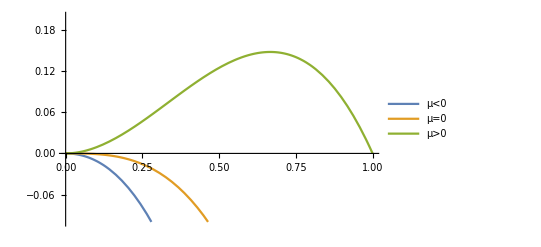

```mathematica
Plot[{f/.μ->-1,f/.μ->0,f/.μ->1},{x,0,1},PlotRange->{{0,1},{-0.1,0.2}},PlotLegends->{"μ<0","μ=0","μ>0"}]
```